# Fang stuff

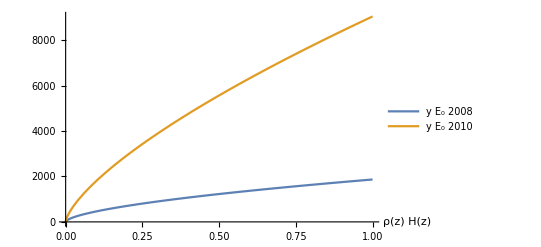

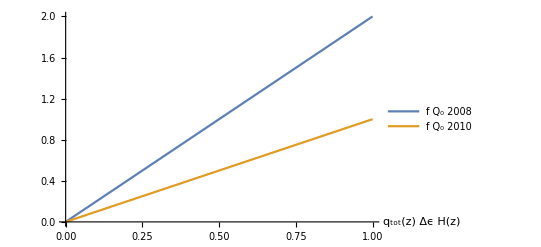

```mathematica
yE0=<|"2008"->(ρH/(4 10^-6))^0.606,"2010"->2(ρH/(6 10^-6))^0.7|>;
fQ0=<|"2008"->2qΔϵH,"2010"->qΔϵH|>;
Plot[{yE0["2008"],yE0["2010"]},{ρH,0,1},PlotLegends->{"y E_0 2008","y E_0 2010"},AxesLabel->{"ρ(z) H(z)",""}]
Plot[{fQ0["2008"],fQ0["2010"]},{qΔϵH,0,1},PlotLegends->{"f Q_0 2008","f Q_0 2010"},AxesLabel->{"q_tot(z) Δϵ H(z)",""}]
```

```mathematica
P=<|"2008"->{{3.49979 10^(−1 ),−6.18200 10^(−2 ),−4.08124 10^(−2 ), 1.65414 10^(−2 )},
{5.85425 10^(−1 ),−5.00793 10^(−2 ), 5.69309 10^(−2 ),−4.02491 10^(−3 )},
{1.69692 10^(−1 ),−2.58981 10^(−2 ), 1.96822 10^(−2 ), 1.20505 10^(−3 )},
{-1.22271 10^(−1 ),−1.15532 10^(−2 ), 5.37951 10^(−6 ), 1.20189 10^(−3 )},
{1.57018 10^(0 ), 2.87896 10^(−1 ),−4.14857 10^(−1 ), 5.18158 10^(−2 )},
{8.83195 10^(−1 ), 4.31402 10^(−2 ),−8.33599 10^(−2 ), 1.02515 10^(−2 )},
{1.90953 10^(0 ),−4.74704 10^(−2 ),−1.80200 10^(−1 ), 2.46652 10^(−2 )},
{−1.29566 10^(0 ),−2.10952 10^(−1 ), 2.73106 10^(−1 ),−2.92752 10^(−2 )}}
,"2010"->{{1.24616 10^(0),1.45903 10^(0),−2.42269 10^(-1),5.95459 10^(-2)},
{2.23976 10^(0),−4.22918 10^(-7),1.36458 10^(-2),2.53332 10^(-3)},
{1.41754 10^(0),1.44597 10^(-1),1.70433 10^(-2),6.39717 10^(-4)},
{2.48775 10^(-1),−1.50890 10^(-1),6.30894 10^(-9),1.23707 10^(-3)},
{−4.65119 10^(-1),−1.05081 10^(-1),−8.95701 10^(-2),1.22450 10^(-2)},
{3.86019 10^(-1),1.75430 10^(-3),−7.42960 10^(-4),4.60881 10^(-4)},
{−6.45454 10^(-1),8.49555 10^(-4),−4.28581 10^(-2),−2.99302 10^(-3)},
{9.48930 10^(-1),1.97385 10^(-1),−2.50660 10^(-3),−2.06938 10^(-3)}}|>;
```

```mathematica
c[i_,E_,v_]:=Exp[Sum[P[[ToString[v]]][[i,j+1]](Log[E])^j,{j,0,3}]]
f[y_,E_,v_]:=c[1,E,v] y^c[2,E,v] Exp[-c[3,E,v] y^c[4,E,v]]+c[5,E,v] y^c[6,E,v] Exp[-c[7,E,v] y^c[8,E,v]]
```

```mathematica
Manipulate[
LogLinearPlot[{
f[y,0.1,2008]
,f[y,1.0001,2008]
,f[y,10,2008]
,f[y,100,2008]
,f[y,1000,2008]
,f[y,0.1,2010]
,f[y,1.0001,2010]
,f[y,10,2010]
,f[y,100,2010]
,f[y,1000,2010]
},{y,0.1,10}
,PlotRange->{All,{0,1}}
,PlotLegends->Flatten[Table[ToString[e]<>" keV "<>ToString[v],{v,{2008,2010}},{e,{0.1,1,10,100,1000}}]]
,ImageSize->Large
,PlotStyle->{
{Black,Opacity[show0p1]}
,Darker@Green
,Brown
,Magenta
,{Red,Opacity[show1000]}
,{Black,Dashed,Opacity[show0p1]}
,{Darker@Green,Dashed}
,{Brown,Dashed}
,{Magenta,Dashed}
,{Red,Dashed,Opacity[show1000]}
},GridLines->Automatic]
,{show1000,{0,1}}
,{show0p1,{0,1}}
]
```

```mathematica
k=1.38064852 10^-16(*cm^2 g s^-2 K^-1*);
G=6.67408 10^-8(*cm^3 g^-1 s^-2*);
ME=5.9722 10^24 10^3(*g*);
RE=6.371 10^6 10^2(*cm*);
mu=1.660539040 10^-27 10^3(*g*);
Δϵ=35 10^-3(*keV*);
erg2kev=6.24150648 10^8;
Q0fang=100(*erg cm^-2 s^-1*);
```

```mathematica
msis=ToExpression[StringSplit/@StringSplit[StringReplace[Import["D:\\Files\\research\\thesis\\msis_maeve_null.lst"],"E"->"*10^"],"
"][[43;;]]];
```

General::munfl: Exp[-397322.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.76806×10^16] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-342789.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

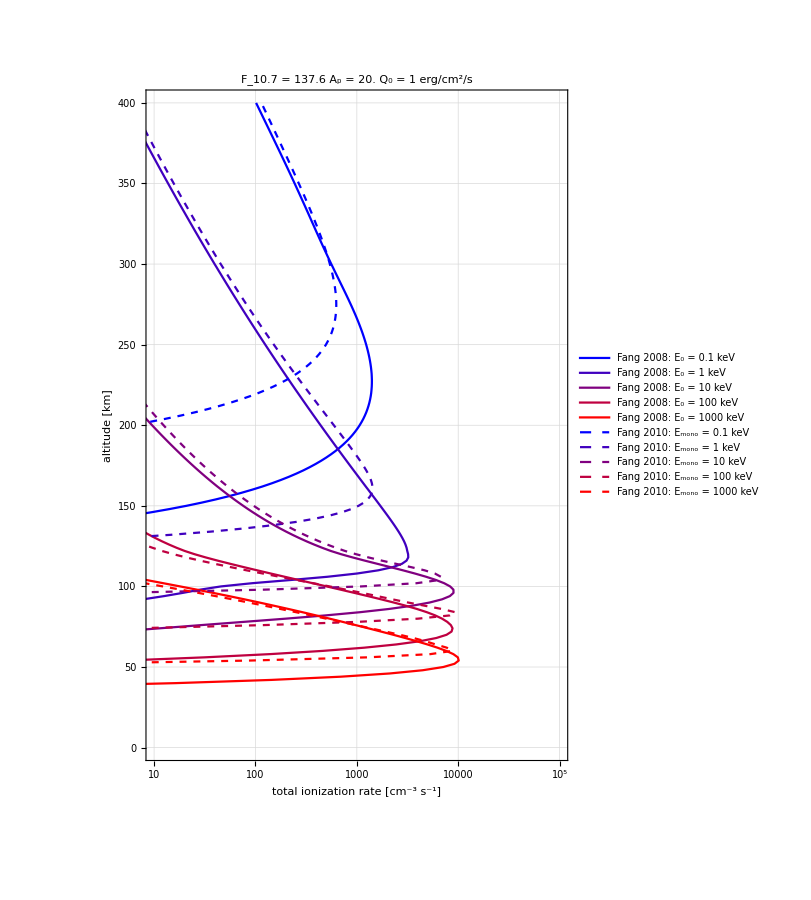

```mathematica
z=msis[[;;,3]] 10^3 10^2(*cm*);
g=(G ME)/(RE+z)^2(*cm s^-2*);
n=msis[[;;,{4,5,6,9,10,11,12}]](*cm^-3*);
ρ=msis[[;;,7]](*g cm^-3*);
m=ρ/(Total/@n) (*g*);
T=msis[[;;,8]](*K*);
H=k T/(m g)(*cm*);
y2008=yE0["2008"]/E0/.ρH->ρ H;
y2010=yE0["2010"]/Emono/.ρH->ρ H;
qtot2008=Q0/(2Δϵ)1/H f[y2008,E0,2008]/.{Q0->Q0fang erg2kev};
qtot2010=Qmono/(2Δϵ)1/H f[y2010,Emono,2010]/.{Qmono->Q0fang erg2kev};
plotA=ListLogLinearPlot[Flatten[Transpose[Table[{
Transpose[{qtot2008/.E0->10^exp,z 10^-5}]
,Transpose[{qtot2010/.Emono->10^exp,z 10^-5}]
},{exp,-1,3}]],1]
,PlotRange->{{10^1,10^5},{0,400}}
,AspectRatio->3/2
,Joined->True
,PlotStyle->Flatten[{Table[RGBColor[s,0,1-s],{s,0,1,1/4}],Table[{RGBColor[s,0,1-s],Dashed},{s,0,1,1/4}]},1]
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,PlotLabel->"F_10.7 = "<>ToString[msis[[1,-2]]] <>" A_p = "<>ToString[msis[[1,-1]]]<>" Q_0 = "<>ToString[Q0fang]<>" erg/cm^2/s"
,GridLines->All
,ImageSize->600
,LabelStyle->Directive[20,Black]
,PlotLegends->Flatten[{
Table["Fang 2008: E_0 = "<>ToString[e]<>" keV",{e,{0.1,1,10,100,1000}}]
,Table["Fang 2010: E_mono = "<>ToString[e]<>" keV",{e,{0.1,1,10,100,1000}}]
}]
]
```

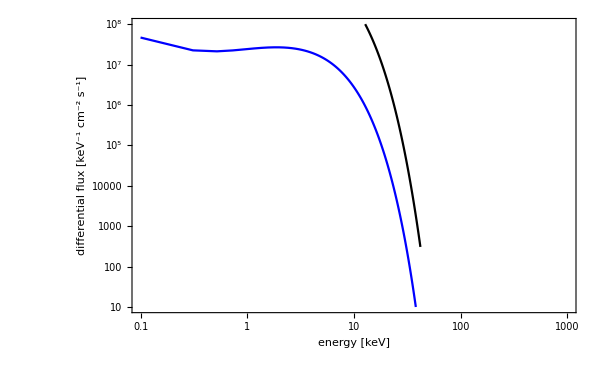

General::munfl: Exp[-18278.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15815.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13613.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

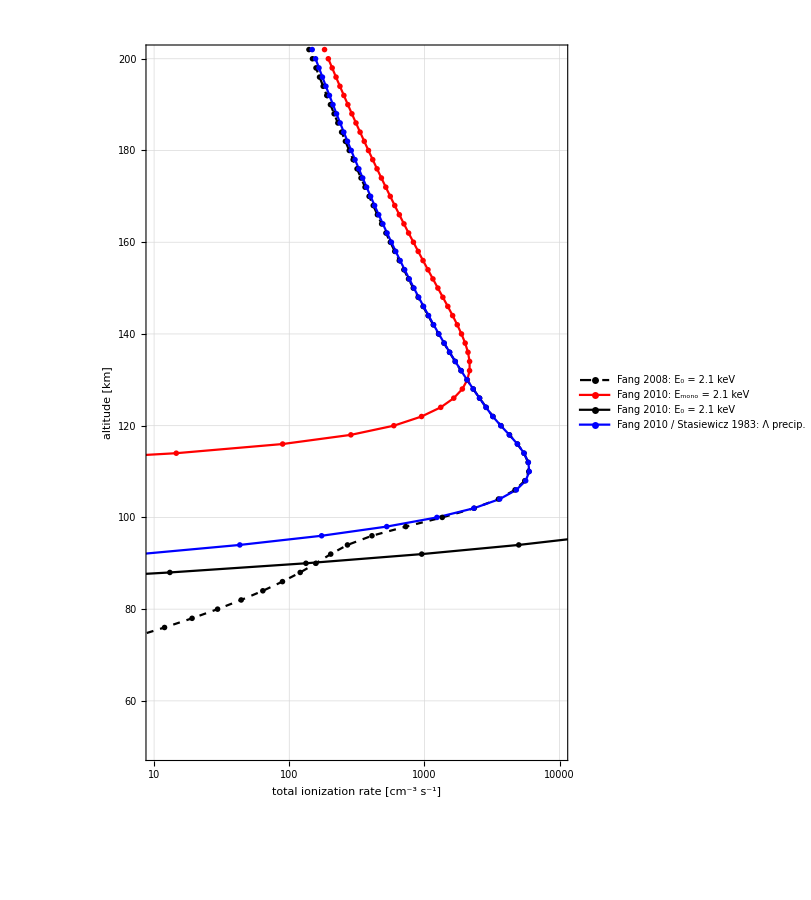

```mathematica
E0spectrum=2.1;
Erange=Range[0.1,20E0spectrum,10E0spectrum/100];
dE=Differences[Erange][[1]];
ϕM=Q0/(2 E0spectrum^3)Emono Exp[-Emono/E0spectrum]/.Q0->100 erg2kev;
ϕMIV=(0.5 10^7)/(1+Exp[Emono-2])Emono^-1+Q0/(2 E0spectrum^3) Emono Exp[-Emono/E0spectrum](1-1/(1+Exp[(-Emono+40)/10]))/.Q0->1 erg2kev;
ϕMdE=ϕM dE (*# of e^- per cm^-2 s^-1 with energies ranging from Subscript[E, mono] to Subscript[E, mono]+dE*);
dQmono=Emono ϕMdE (*energy flux (keV/cm^2/s) of e^- with energy Subscript[E, mono]*);
dQmonoIV=Emono ϕMIV dE;
qtotspectrum=Total[Transpose[dQmono/Δϵ 1/H f[y2010,Emono,2010]/.Emono->Erange]];
qtotspectrumIV=Total[Transpose[dQmonoIV/Δϵ 1/H f[y2010,Emono,2010]/.Emono->Erange]];
plotC=ListLogLogPlot[{
Transpose[{Erange,ϕM/.Emono->Erange}]
,Transpose[{Erange,ϕMIV/.Emono->Erange}]
}
,Joined->True
,GridLines->All
,PlotRange->{{10^-1,10^3},{10^1,10^8}}
,PlotStyle->{Black,Blue}
,Frame->True
,FrameLabel->{"energy [keV]","differential flux [keV^-1 cm^-2 s^-1]"}
,ImageSize->600
,LabelStyle->Directive[20,Black]
]
plotB=ListLogLinearPlot[{
Transpose[{qtot2008/.E0->E0spectrum,z 10^-5}]
,Transpose[{qtot2010/.Emono->E0spectrum,z 10^-5}]
,Transpose[{qtotspectrum,z 10^-5}]
,Transpose[{qtotspectrumIV,z 10^-5}]
}
,PlotRange->{{10^1,10^4},{50,200}}
,AspectRatio->3/2
,Joined->True
,PlotMarkers->"OpenMarkers"
,PlotStyle->{{Black,Dashed},Red,Black,Blue}
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,GridLines->All
,PlotLegends->{"Fang 2008: E_0 = "<>ToString[E0spectrum]<>" keV","Fang 2010: E_mono = "<>ToString[E0spectrum]<>" keV","Fang 2010: E_0 = "<>ToString[E0spectrum]<>" keV","Fang 2010 / Stasiewicz 1983: Λ precip."}
,ImageSize->600
,LabelStyle->Directive[20,Black]
]
```

```mathematica
Export[NotebookDirectory[]<>"FangComparisonMaxMono.png",plotA]
Export[NotebookDirectory[]<>"FangComparisonMaxMonoMax.png",plotB]
Export[NotebookDirectory[]<>"FangComparisonSpectra.png",plotC]
```

D:\Files\research\thesis\FangComparisonMaxMono.png

D:\Files\research\thesis\FangComparisonMaxMonoMax.png

D:\Files\research\thesis\FangComparisonSpectra.png

## The above demonstrates the proper use of Fang 2010 is by doing the following: with E⧦E_mono and Q⧦Q_mono q_tot(z)=∫dq_tot(z)=∫(dQ(E))/(Δϵ H)f(y(z,E),E) dQ(E)=Eϕ_Mx(E,Q_0,E_0)dE y(z,E)=2/E((ρ(z)H(z))/(6 10^-6))^0.7 Doing this with ϕ_Mx(E,Q_0,E_0) being a Maxwellian from Fang 2008 gets you the same results.